```mathematica
(* Student Name *)
(* July 14, 2017 *)
(* MITES Physics III: Intro to Oscillations and Waves *)
(* Predator and Prey Oscillations*)

(* Euler Method Solution of Lynx and Hare differential equations *)
```

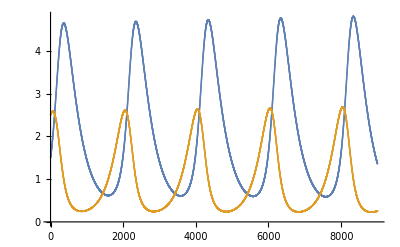

```mathematica
l0 = 1.5; (* Defines the initial value of the lynx array *) 

h0 = 2.5; (* Defines the initial value of the hare array *) 

e = 0.001; (* Defines how much we increment by time *) 

α = 4; β = 2; γ = 3; δ  = 3;

lvalues= ConstantArray[0,9000]; (* Defines an empty array of values for our lynxes *) 

hvalues= ConstantArray[0,9000]; (* Defines an empty array of values for our hares *) 

lvalues[[1]] = l0; (* Sets first value of lynx array to defined initial lynx number *) 

hvalues[[1]] = h0; (* Sets first value of hare arraty to defined initial hare number *) 

For[i=2, (* Sets initial value of for loop *) 
i<9001, (* Condition for for increment of for loop *) 
i++, (* Increment for loop by a single index *) 
lvalues[[i]] = lvalues[[i-1]]+e*(δ* hvalues[[i-1]]*lvalues[[i-1]]-  γ *lvalues[[i-1]] )   ; (* Defines next l value as a first order Taylor series approximation of the lynx population *) 
hvalues[[i]] = hvalues[[i-1]]+ e*(α *hvalues[[i-1]]- β* hvalues[[i-1]]*lvalues[[i-1]] ) ] (* Defines next h value value as a first order Taylor series approximation of the hare population *) 
ListPlot[{ lvalues,hvalues}] (* Plots the list of hvalues and lvalues to  *)
```